# Proyecto

## Novoa Gastaldi Alejandro Silvestre

(silvestre.novoa@ciencias.unam.mx)

## ------

```mathematica
Clear["Global`*"]


Zigzag=4.;
Armchair=4.;

NZigzag=1.+2*Zigzag;
NArmchair=2*Armchair;

NEdos=1*NZigzag*NArmchair;

t=-1.;





 (*   Notacion {n;...} ={0,...,0,1,0,...,0;...}  *)

Base= Table[   Table[   -0.   ,{i,1,6}]    ,{j,1,1}];

Base =Flatten[    Table[       Base      ,{i,1, NZigzag*NArmchair ,1}]    ,1];
Do[          Do[       Base[[i,1]]=j       ,{i,1+1*(j-1),1+1*(j-1),1}]         ,{j,1.,NZigzag*NArmchair ,1.}];

Print[     Style["Base ",18,Bold,Purple]      ]
MatrixForm[   Base  ]
```

Base

(1. | 0. | 0. | 0. | 0. | 0.
2. | 0. | 0. | 0. | 0. | 0.
3. | 0. | 0. | 0. | 0. | 0.
4. | 0. | 0. | 0. | 0. | 0.
5. | 0. | 0. | 0. | 0. | 0.
6. | 0. | 0. | 0. | 0. | 0.
7. | 0. | 0. | 0. | 0. | 0.
8. | 0. | 0. | 0. | 0. | 0.
9. | 0. | 0. | 0. | 0. | 0.
10. | 0. | 0. | 0. | 0. | 0.
11. | 0. | 0. | 0. | 0. | 0.
12. | 0. | 0. | 0. | 0. | 0.
13. | 0. | 0. | 0. | 0. | 0.
14. | 0. | 0. | 0. | 0. | 0.
15. | 0. | 0. | 0. | 0. | 0.
16. | 0. | 0. | 0. | 0. | 0.
17. | 0. | 0. | 0. | 0. | 0.
18. | 0. | 0. | 0. | 0. | 0.
19. | 0. | 0. | 0. | 0. | 0.
20. | 0. | 0. | 0. | 0. | 0.
21. | 0. | 0. | 0. | 0. | 0.
22. | 0. | 0. | 0. | 0. | 0.
23. | 0. | 0. | 0. | 0. | 0.
24. | 0. | 0. | 0. | 0. | 0.
25. | 0. | 0. | 0. | 0. | 0.
26. | 0. | 0. | 0. | 0. | 0.
27. | 0. | 0. | 0. | 0. | 0.
28. | 0. | 0. | 0. | 0. | 0.
29. | 0. | 0. | 0. | 0. | 0.
30. | 0. | 0. | 0. | 0. | 0.
31. | 0. | 0. | 0. | 0. | 0.
32. | 0. | 0. | 0. | 0. | 0.
33. | 0. | 0. | 0. | 0. | 0.
34. | 0. | 0. | 0. | 0. | 0.
35. | 0. | 0. | 0. | 0. | 0.
36. | 0. | 0. | 0. | 0. | 0.
37. | 0. | 0. | 0. | 0. | 0.
38. | 0. | 0. | 0. | 0. | 0.
39. | 0. | 0. | 0. | 0. | 0.
40. | 0. | 0. | 0. | 0. | 0.
41. | 0. | 0. | 0. | 0. | 0.
42. | 0. | 0. | 0. | 0. | 0.
43. | 0. | 0. | 0. | 0. | 0.
44. | 0. | 0. | 0. | 0. | 0.
45. | 0. | 0. | 0. | 0. | 0.
46. | 0. | 0. | 0. | 0. | 0.
47. | 0. | 0. | 0. | 0. | 0.
48. | 0. | 0. | 0. | 0. | 0.
49. | 0. | 0. | 0. | 0. | 0.
50. | 0. | 0. | 0. | 0. | 0.
51. | 0. | 0. | 0. | 0. | 0.
52. | 0. | 0. | 0. | 0. | 0.
53. | 0. | 0. | 0. | 0. | 0.
54. | 0. | 0. | 0. | 0. | 0.
55. | 0. | 0. | 0. | 0. | 0.
56. | 0. | 0. | 0. | 0. | 0.
57. | 0. | 0. | 0. | 0. | 0.
58. | 0. | 0. | 0. | 0. | 0.
59. | 0. | 0. | 0. | 0. | 0.
60. | 0. | 0. | 0. | 0. | 0.
61. | 0. | 0. | 0. | 0. | 0.
62. | 0. | 0. | 0. | 0. | 0.
63. | 0. | 0. | 0. | 0. | 0.
64. | 0. | 0. | 0. | 0. | 0.
65. | 0. | 0. | 0. | 0. | 0.
66. | 0. | 0. | 0. | 0. | 0.
67. | 0. | 0. | 0. | 0. | 0.
68. | 0. | 0. | 0. | 0. | 0.
69. | 0. | 0. | 0. | 0. | 0.
70. | 0. | 0. | 0. | 0. | 0.
71. | 0. | 0. | 0. | 0. | 0.
72. | 0. | 0. | 0. | 0. | 0.)

Set::write: Tag Times in ⅈ {{0.,-1.,0.,0.,0.,0.,0.,0.,0.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«22»},{-1.,0.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«22»},«48»,«22»} is Protected.

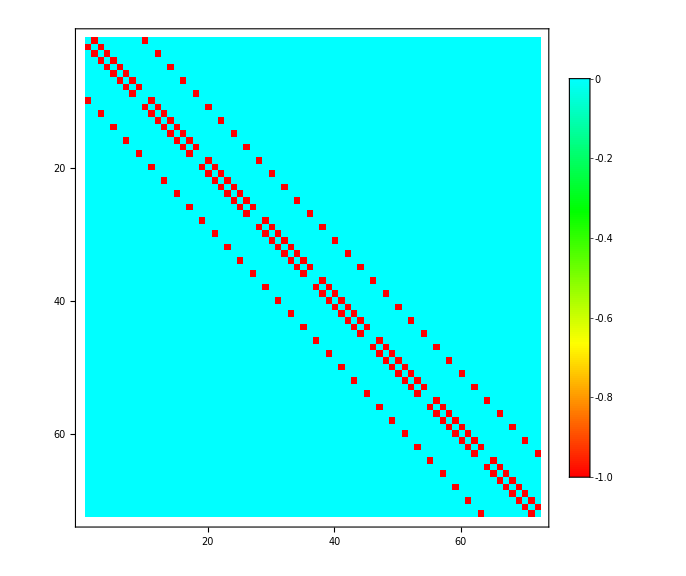

{{2.85911},{{0.0235754,-0.0298333,0.0617212,-0.0482713,0.0762916,-0.0482713,0.0617212,-0.0298333,0.0235754,-0.0375713,0.0838451,-0.098363,0.135664,-0.121583,0.135664,-0.098363,0.0838451,-0.0375713,0.0588429,-0.103788,0.154053,-0.167932,0.19042,-0.167932,0.154053,-0.103788,0.0588429,-0.0644503,0.125428,-0.168733,0.202946,-0.208566,0.202946,-0.168733,0.125428,-0.0644503,0.0644503,-0.125428,0.168733,-0.202946,0.208566,-0.202946,0.168733,-0.125428,0.0644503,-0.0588429,0.103788,-0.154053,0.167932,-0.19042,0.167932,-0.154053,0.103788,-0.0588429,0.0375713,-0.0838451,0.098363,-0.135664,0.121583,-0.135664,0.098363,-0.0838451,0.0375713,-0.0235754,0.0298333,-0.0617212,0.0482713,-0.0762916,0.0482713,-0.0617212,0.0298333,-0.0235754}}}

Energias Numericas

(2.85911)

Energias Exactas

{{En→-2.85923 t1},{En→-2.72777 t1},{En→-2.63632 t1},{En→(-2.53328-0.116669 ⅈ) t1},{En→(-2.53328+0.116669 ⅈ) t1},{En→(-2.35283-0.202545 ⅈ) t1},{En→(-2.35283+0.202545 ⅈ) t1},{En→(-2.15729-0.266044 ⅈ) t1},{En→(-2.15729+0.266044 ⅈ) t1},{En→(-1.95512-0.289793 ⅈ) t1},{En→(-1.95512+0.289793 ⅈ) t1},{En→(-1.75338-0.279317 ⅈ) t1},{En→(-1.75338+0.279317 ⅈ) t1},{En→-1.59922 t1},{En→(-1.5669-0.251103 ⅈ) t1},{En→(-1.5669+0.251103 ⅈ) t1},{En→(-1.40334-0.138558 ⅈ) t1},{En→(-1.40334+0.138558 ⅈ) t1},{En→(-1.38489-0.223217 ⅈ) t1},{En→(-1.38489+0.223217 ⅈ) t1},{En→-1.36007 t1},{En→(-1.23802-0.242747 ⅈ) t1},{En→(-1.23802+0.242747 ⅈ) t1},{En→(-1.12409-0.242117 ⅈ) t1},{En→(-1.12409+0.242117 ⅈ) t1},{En→(-1.03483-0.222828 ⅈ) t1},{En→(-1.03483+0.222828 ⅈ) t1},{En→-1.00442 t1},{En→(-0.973345-0.191176 ⅈ) t1},{En→(-0.973345+0.191176 ⅈ) t1},{En→-0.945638 t1},{En→(-0.928138-0.169418 ⅈ) t1},{En→(-0.928138+0.169418 ⅈ) t1},{En→(-0.874899-0.138161 ⅈ) t1},{En→(-0.874899+0.138161 ⅈ) t1},{En→(-0.828222-0.0881248 ⅈ) t1},{En→(-0.828222+0.0881248 ⅈ) t1},{En→(-0.776174-0.0187978 ⅈ) t1},{En→(-0.776174+0.0187978 ⅈ) t1},{En→-0.725686 t1},{En→-0.649652 t1},{En→-0.524734 t1},{En→-0.32382 t1},{En→-0.013183 t1},{En→0.013183 t1},{En→0.32382 t1},{En→0.524734 t1},{En→0.649652 t1},{En→0.725686 t1},{En→(0.776174-0.0187978 ⅈ) t1},{En→(0.776174+0.0187978 ⅈ) t1},{En→(0.828222-0.0881248 ⅈ) t1},{En→(0.828222+0.0881248 ⅈ) t1},{En→(0.874899-0.138161 ⅈ) t1},{En→(0.874899+0.138161 ⅈ) t1},{En→(0.928138-0.169418 ⅈ) t1},{En→(0.928138+0.169418 ⅈ) t1},{En→0.945638 t1},{En→(0.973345-0.191176 ⅈ) t1},{En→(0.973345+0.191176 ⅈ) t1},{En→1.00442 t1},{En→(1.03483-0.222828 ⅈ) t1},{En→(1.03483+0.222828 ⅈ) t1},{En→(1.12409-0.242117 ⅈ) t1},{En→(1.12409+0.242117 ⅈ) t1},{En→(1.23802-0.242747 ⅈ) t1},{En→(1.23802+0.242747 ⅈ) t1},{En→1.36007 t1},{En→(1.38489-0.223217 ⅈ) t1},{En→(1.38489+0.223217 ⅈ) t1},{En→(1.40334-0.138558 ⅈ) t1},{En→(1.40334+0.138558 ⅈ) t1},{En→(1.5669-0.251103 ⅈ) t1},{En→(1.5669+0.251103 ⅈ) t1},{En→1.59922 t1},{En→(1.75338-0.279317 ⅈ) t1},{En→(1.75338+0.279317 ⅈ) t1},{En→(1.95512-0.289793 ⅈ) t1},{En→(1.95512+0.289793 ⅈ) t1},{En→(2.15729-0.266044 ⅈ) t1},{En→(2.15729+0.266044 ⅈ) t1},{En→(2.35283-0.202545 ⅈ) t1},{En→(2.35283+0.202545 ⅈ) t1},{En→(2.53328-0.116669 ⅈ) t1},{En→(2.53328+0.116669 ⅈ) t1},{En→2.63632 t1},{En→2.72777 t1},{En→2.85923 t1}}

```mathematica
(********************* ----- HAMILTONIANO en Espacio de Estados ----- *********************)


HEdoBase=Table[Table[  0.  ,{i,1,NEdos,1}],{j,1,NEdos,1}];



(* NO DIAGONAL:  Transicion entre sitios*)

(*Transporte entre sitios*)
Base[[1]];
Base[[1+1]];
Base[[1]]+UnitVector[6,1] ;    (*   Notacion:  Subscript[b, n+1]^† Subscript[b, n] {n;...} = √1 √(0+1){0,...,0,1-1,0+1,...,0;...} = {n+1;...} *)


Do[  Do[  HEdoBase[[i,i+1]]=t  ,{i,    1 + 1*NZigzag*(j-1)  ,   1* (    NZigzag-1 +(j-1)*NZigzag    )     ,1}]  , {j,1,NArmchair,1} ]   (*Para interacciones entre filas  {n;...} y {n+1;...} en direccion zigzag *)


Do[  Do[  HEdoBase[[    i+1*(j-1),   i+1*(j-1+NZigzag)  ]]=t  ,{i,    1  ,   1    ,1}]  , {j,1,    (NArmchair-1)*NZigzag     ,2} ]   (*Para interacciones entre filas  {n;...} y {n+1;...} en direccion zigzag *)




HEdoBase  =(HEdoBase+ConjugateTranspose[HEdoBase]);




(* Se ingresa las posiciones atomicas que actuaran de Fuente y Drenante *)
PosicionFuente=Table[   i   ,{i,1,NZigzag,1}];     (*Table[   i   ,{i,1,NZigzag,1}]*)
PosicionDrentante=Table[   NEdos-NZigzag+i   ,{i,1,NZigzag,1}];

PosicionFuente=  Table   [    Round[{PosicionFuente[[i]] , PosicionFuente[[i]] }]    ,{i,1, Length[PosicionFuente],1}];              (* Genera las posiciones correspondientes a la matriz *)
PosicionDrentante=  Table   [    Round[{PosicionDrentante[[i]] , PosicionDrentante[[i]] }]    ,{i,1, Length[PosicionDrentante],1}];

(* Matrices de Autoenergías *)
SigmaFuente=-ⅈ *tF *SparseArray[{        PosicionFuente->Table[1. , {i,1, Length[PosicionFuente],1} ]        },{NEdos,NEdos}];
SigmaDrenante= -ⅈ*tD*SparseArray[{        PosicionDrentante->Table[1. , {i,1, Length[PosicionDrentante],1} ]        },{NEdos,NEdos}];



HEdoBase I =HEdoBase -SigmaDrenante;



HEdoBase // MatrixForm;
MatrixPlot[HEdoBase ,PlotTheme->"Detailed",ImageSize->Large,ColorFunction->Hue]


(*  Solución Numerica   *)
{eval,evec}=Eigensystem[HEdoBase,  1,Method->{"Arnoldi","Criteria"->"RealPart"} ]

Print[     Style["Energias Numericas ",18,Bold,Purple]      ]
Style[    MatrixForm[  eval  ]   ,{Medium,Bold,Purple}]



(*  Solución Exacta:    Usa el mismo hamiltoniano de interacción   *)

t1*HEdoBase   // MatrixForm;

Print[     Style["Energias Exactas ",18,Bold,Purple]      ]
Quiet[        Solve[   Det[           t1*HEdoBase-En*IdentityMatrix[   Round[NEdos]    ]          ]==0    ,En]          ]

(*Eigenfunction*)
```

```mathematica
(********************* ----- HAMILTONIANO en Espacio Real ----- *********************)

(*Para este problema simplificado queda identico*)

HReal = HEdoBase ;
HEdoBase // MatrixForm;
MatrixPlot[HEdoBase ,PlotTheme->"Detailed",ImageSize->Large,ColorFunction->Hue]


(* Para usar Green se requiere el Hamiltoniano discretiado (Matriz) en el espacio Real *)


(* Con Green obtendremos observables en función de la energía *)
Energia=En*IdentityMatrix[   Round[NEdos]    ];


(* Se ingresa las posiciones atomicas que actuaran de Fuente y Drenante *)
PosicionFuente=Table[   i   ,{i,1,NZigzag,1}];     (*Table[   i   ,{i,1,NZigzag,1}]*)
PosicionDrentante=Table[   NEdos-NZigzag+i   ,{i,1,NZigzag,1}];

PosicionFuente=  Table   [    Round[{PosicionFuente[[i]] , PosicionFuente[[i]] }]    ,{i,1, Length[PosicionFuente],1}];              (* Genera las posiciones correspondientes a la matriz *)
PosicionDrentante=  Table   [    Round[{PosicionDrentante[[i]] , PosicionDrentante[[i]] }]    ,{i,1, Length[PosicionDrentante],1}];

(* Matrices de Autoenergías *)
SigmaFuente=-ⅈ *tF *SparseArray[{        PosicionFuente->Table[1. , {i,1, Length[PosicionFuente],1} ]        },{NEdos,NEdos}];
SigmaDrenante= -ⅈ*tD*SparseArray[{        PosicionDrentante->Table[1. , {i,1, Length[PosicionDrentante],1} ]        },{NEdos,NEdos}];


tF=1.;
tD=1.;
t1=1.;
```

-Graphics-

(0. | 0.00140666 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00177152 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00140666 | 0. | 0.00368269 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.00368269 | 0. | 0.00595872 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0121422 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.00595872 | 0. | 0.00736538 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.00736538 | 0. | 0.00736538 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0185516 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.00736538 | 0. | 0.00595872 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.00595872 | 0. | 0.00368269 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0121422 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.00368269 | 0. | 0.00140666 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00140666 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00177152 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00177152 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00630034 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00630034 | 0. | 0.0164945 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0174042 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0121422 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0164945 | 0. | 0.0266887 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0266887 | 0. | 0.032989 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0455648 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.0185516 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.032989 | 0. | 0.032989 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.032989 | 0. | 0.0266887 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0455648 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0121422 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0266887 | 0. | 0.0164945 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0164945 | 0. | 0.00630034 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0174042 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00177152 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00630034 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0122143 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00758489 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0174042 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0122143 | 0. | 0.0319776 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0319776 | 0. | 0.0517408 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0519876 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0455648 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0517408 | 0. | 0.0639552 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0639552 | 0. | 0.0639552 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.07943 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0455648 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0639552 | 0. | 0.0517408 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0517408 | 0. | 0.0319776 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0519876 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0174042 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0319776 | 0. | 0.0122143 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0122143 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00758489 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00758489 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0161677 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0161677 | 0. | 0.0423276 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0314642 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0519876 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0423276 | 0. | 0.0684875 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0684875 | 0. | 0.0846552 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0823743 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.07943 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0846552 | 0. | 0.0846552 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0846552 | 0. | 0.0684875 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0823743 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0519876 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0684875 | 0. | 0.0423276 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0423276 | 0. | 0.0161677 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0314642 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00758489 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0161677 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0161677 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00758489 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0314642 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0161677 | 0. | 0.0423276 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0423276 | 0. | 0.0684875 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0519876 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0823743 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0684875 | 0. | 0.0846552 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0846552 | 0. | 0.0846552 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.07943 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0823743 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0846552 | 0. | 0.0684875 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0684875 | 0. | 0.0423276 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0519876 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0314642 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0423276 | 0. | 0.0161677 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0161677 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00758489 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00758489 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0122143 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0122143 | 0. | 0.0319776 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0174042 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0519876 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0319776 | 0. | 0.0517408 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0517408 | 0. | 0.0639552 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0455648 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.07943 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0639552 | 0. | 0.0639552 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0639552 | 0. | 0.0517408 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0455648 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0519876 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0517408 | 0. | 0.0319776 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0319776 | 0. | 0.0122143 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0174042 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00758489 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0122143 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00630034 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00177152 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0174042 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00630034 | 0. | 0.0164945 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0164945 | 0. | 0.0266887 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0121422 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0455648 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0266887 | 0. | 0.032989 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.032989 | 0. | 0.032989 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0185516 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0455648 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.032989 | 0. | 0.0266887 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0266887 | 0. | 0.0164945 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0121422 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0174042 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0164945 | 0. | 0.00630034 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00630034 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00177152
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00177152 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00140666 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00140666 | 0. | 0.00368269 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0121422 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00368269 | 0. | 0.00595872 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00595872 | 0. | 0.00736538 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0185516 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00736538 | 0. | 0.00736538 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00736538 | 0. | 0.00595872 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0121422 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00595872 | 0. | 0.00368269 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00368269 | 0. | 0.00140666
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00177152 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00140666 | 0.)

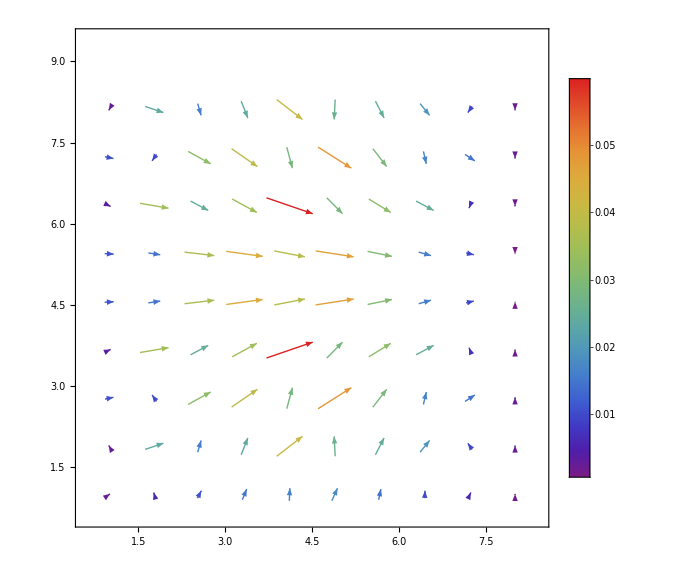

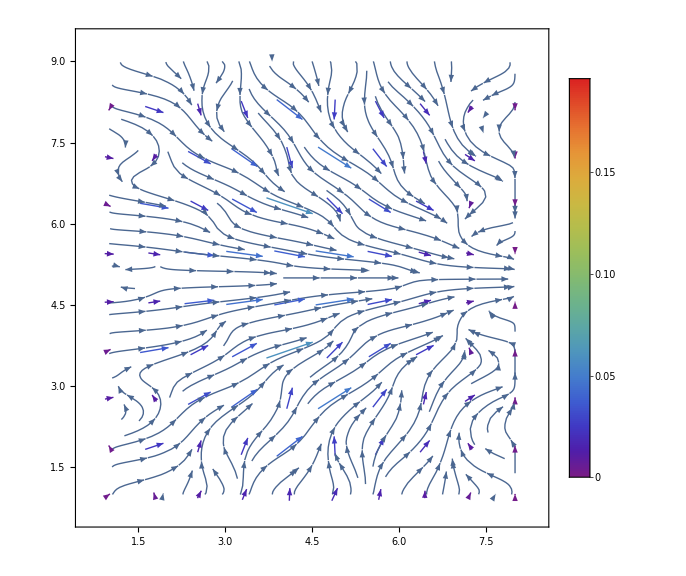

```mathematica
(********************* ----- I Operador ----- *********************)

eval[[1]];
EdoBase=evec[[1]];


(*    Subscript[I, i] = ⅈ*(e/h)*2*π*( H Gn - Gn H )         Notacion:  Subscript[b, n+1]^† Subscript[b, n] {n;...} = √1 √(0+1){0,...,0,1-1,0+1,...,0;...} = {n+1;...} *)
(HEdoBase- SigmaFuente  -  SigmaDrenante) *GnMatrizDensidad // MatrixForm;

GnMatrizDensidad=Table[    Table[   Conjugate[  EdoBase[[ j ]]  ]*EdoBase[[ i ]]   ,{i,1,NEdos,1}]   ,{j,1,NEdos,1}];
GnMatrizDensidad // MatrixForm;

IOperador=ⅈ*(   ( HEdoBase    +  SigmaDrenante) *GnMatrizDensidad   +   GnMatrizDensidad   * ( HEdoBase  +  SigmaDrenante)   ) ;

IVal=Im[IOperador];
IVal// MatrixForm





ILocalY=Table[         Table[     -IVal[[il,  (jl-1)*NZigzag+Mod[il-1,NZigzag,1]  ]]+ IVal[[il, (jl-1)*NZigzag+Mod[il+1,NZigzag,1]   ]]     , {il, 1+(jl-1)*NZigzag,jl*NZigzag,1}]    , {jl,1,NArmchair,1}];
ILocalY=Flatten[ ILocalY];

ILocalX=   Join[     Table[    IVal[[il,il+NZigzag ]]     ,{il,1,NZigzag*(NArmchair-1),1}  ] , Table[ 0., {jl,1,NZigzag,1}]      ];



ILocal=              Table[  {       {  1.+IntegerPart[   (i-1)/(NZigzag ) ],  Mod[ i,NZigzag,1.]     }   ,       {ILocalX[[i]],  ILocalY[[i]] }    } ,   {i,1, NEdos,1.}];     


ListVectorPlot[      ILocal     ,ImageSize->Large, VectorColorFunction->"Rainbow",VectorPoints->10, VectorScale->0.08, PlotLegends->Automatic]
ListStreamPlot[      ILocal     ,ImageSize->Large, VectorColorFunction->"Rainbow", VectorPoints->10, VectorScale->0.08, PlotLegends->Automatic]


Clear[En]


(*    Subscript[J, i] = 2*J*( Subscript[b, i+1]^† Subscript[b, i] - Subscript[b, i-1]^† Subscript[b, i])         Notacion:  Subscript[b, n+1]^† Subscript[b, n] {n;...} = √1 √(0+1){0,...,0,1-1,0+1,...,0;...} = {n+1;...} *)
```

```mathematica
(* Con Green obtendremos observables en función de la energía *)
EnMin=-4.;
EnMax=4.;
NEnPuntos=501.;

DEn = Abs[EnMax-EnMin]/ (NEnPuntos-1.);
EnergiasValores=Table [   ( i )      ,{i,EnMin,EnMax,DEn}     ];


Energia=    Table [   ( i )*IdentityMatrix[   Round[NEdos]    ]       ,{i,EnMin,EnMax,DEn}     ];





(*Broadening Matrix*)
GammaFuente = ⅈ*(  SigmaFuente -ConjugateTranspose[  SigmaFuente ]);
GammaDrenante= ⅈ*(  SigmaDrenante -ConjugateTranspose[  SigmaDrenante ]);





(*Funcion de Green del Nanosistema*)
FGreen= Table[        Inverse[  Energia [[i]]  -  HEdoBase  - SigmaFuente  -  SigmaDrenante   ]       , {i,1,NEnPuntos,1}];
```

Función de Transmisión

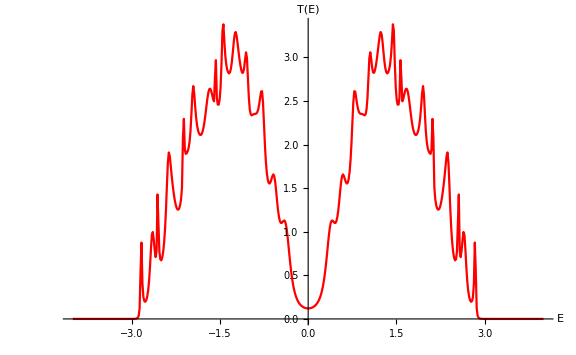

DOS

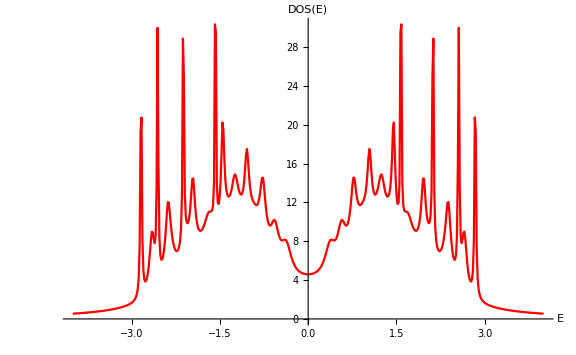

LDOS

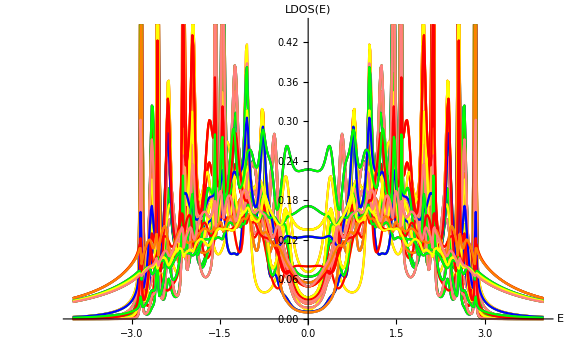

```mathematica
(*Funcion de Transmision*)
Print[     Style["Función de Transmisión",18,Bold,Purple]      ]
FTranmision= Table[          { EnMin  +  DEn*(i-1)   ,      Tr[     GammaDrenante.  FGreen[[i]]  .GammaFuente.ConjugateTranspose[   FGreen[[i]]  ]     ]  }      , {i,1,NEnPuntos,1}];

ListPlot[     FTranmision    ,PlotStyle->{{PointSize[0.01],Red}},LabelStyle->{14,Black},AxesLabel->{"E" ,"T(E)"}, ImageSize->Large,   Joined->True]






(*Función Espectral*)
A=   Table[         ⅈ*(  FGreen[[i]]  -  ConjugateTranspose[  FGreen[[i]]  ]  )       , {i,1,NEnPuntos,1}];



(*DOS: Densidad de Estados*)
Print[     Style["DOS",18,Bold,Purple]      ]
DOS=    Table[        { EnMin  +  DEn*(i-1)   ,       Re[   Tr[  A[[i]]  ]/(2*π)   ]   }     , {i,1,NEnPuntos,1}];

ListPlot[     DOS    ,PlotStyle->{{PointSize[0.01],Red}},LabelStyle->{14,Black},AxesLabel->{"E" ,"DOS(E)"}, ImageSize->Large,   Joined->True]


(*LDOS: Densidad Local de Estados*)
Print[     Style["LDOS",18,Bold,Purple]      ]
LDOS=    Table[              Re[  Diagonal[  A[[i]]   ]/(2*π)  ]           , {i,1,NEnPuntos,1}];     (*Los elementos de la Diagonal de A *)

LDOSSitios=Table[                   Table[         { EnMin  +  DEn*(i-1)   ,         LDOS[[i,j]]   }       ,     {i,1,NEnPuntos,1}]                   ,     {j,1,NEdos,1}] ;
ListPlot[     LDOSSitios     ,PlotStyle->{{PointSize[0.012],Blue},{PointSize[0.015],Red},{PointSize[0.01],Green},{PointSize[0.006],Orange},{PointSize[0.003],Yellow},{PointSize[0.008],Pink}},LabelStyle->{14,Black},AxesLabel->{"E" ,"LDOS(E)"}, ImageSize->Large,   Joined->True]
```

```mathematica
EnergiasValores
```

{-4.,-3.984,-3.968,-3.952,-3.936,-3.92,-3.904,-3.888,-3.872,-3.856,-3.84,-3.824,-3.808,-3.792,-3.776,-3.76,-3.744,-3.728,-3.712,-3.696,-3.68,-3.664,-3.648,-3.632,-3.616,-3.6,-3.584,-3.568,-3.552,-3.536,-3.52,-3.504,-3.488,-3.472,-3.456,-3.44,-3.424,-3.408,-3.392,-3.376,-3.36,-3.344,-3.328,-3.312,-3.296,-3.28,-3.264,-3.248,-3.232,-3.216,-3.2,-3.184,-3.168,-3.152,-3.136,-3.12,-3.104,-3.088,-3.072,-3.056,-3.04,-3.024,-3.008,-2.992,-2.976,-2.96,-2.944,-2.928,-2.912,-2.896,-2.88,-2.864,-2.848,-2.832,-2.816,-2.8,-2.784,-2.768,-2.752,-2.736,-2.72,-2.704,-2.688,-2.672,-2.656,-2.64,-2.624,-2.608,-2.592,-2.576,-2.56,-2.544,-2.528,-2.512,-2.496,-2.48,-2.464,-2.448,-2.432,-2.416,-2.4,-2.384,-2.368,-2.352,-2.336,-2.32,-2.304,-2.288,-2.272,-2.256,-2.24,-2.224,-2.208,-2.192,-2.176,-2.16,-2.144,-2.128,-2.112,-2.096,-2.08,-2.064,-2.048,-2.032,-2.016,-2.,-1.984,-1.968,-1.952,-1.936,-1.92,-1.904,-1.888,-1.872,-1.856,-1.84,-1.824,-1.808,-1.792,-1.776,-1.76,-1.744,-1.728,-1.712,-1.696,-1.68,-1.664,-1.648,-1.632,-1.616,-1.6,-1.584,-1.568,-1.552,-1.536,-1.52,-1.504,-1.488,-1.472,-1.456,-1.44,-1.424,-1.408,-1.392,-1.376,-1.36,-1.344,-1.328,-1.312,-1.296,-1.28,-1.264,-1.248,-1.232,-1.216,-1.2,-1.184,-1.168,-1.152,-1.136,-1.12,-1.104,-1.088,-1.072,-1.056,-1.04,-1.024,-1.008,-0.992,-0.976,-0.96,-0.944,-0.928,-0.912,-0.896,-0.88,-0.864,-0.848,-0.832,-0.816,-0.8,-0.784,-0.768,-0.752,-0.736,-0.72,-0.704,-0.688,-0.672,-0.656,-0.64,-0.624,-0.608,-0.592,-0.576,-0.56,-0.544,-0.528,-0.512,-0.496,-0.48,-0.464,-0.448,-0.432,-0.416,-0.4,-0.384,-0.368,-0.352,-0.336,-0.32,-0.304,-0.288,-0.272,-0.256,-0.24,-0.224,-0.208,-0.192,-0.176,-0.16,-0.144,-0.128,-0.112,-0.096,-0.08,-0.064,-0.048,-0.032,-0.016,0.,0.016,0.032,0.048,0.064,0.08,0.096,0.112,0.128,0.144,0.16,0.176,0.192,0.208,0.224,0.24,0.256,0.272,0.288,0.304,0.32,0.336,0.352,0.368,0.384,0.4,0.416,0.432,0.448,0.464,0.48,0.496,0.512,0.528,0.544,0.56,0.576,0.592,0.608,0.624,0.64,0.656,0.672,0.688,0.704,0.72,0.736,0.752,0.768,0.784,0.8,0.816,0.832,0.848,0.864,0.88,0.896,0.912,0.928,0.944,0.96,0.976,0.992,1.008,1.024,1.04,1.056,1.072,1.088,1.104,1.12,1.136,1.152,1.168,1.184,1.2,1.216,1.232,1.248,1.264,1.28,1.296,1.312,1.328,1.344,1.36,1.376,1.392,1.408,1.424,1.44,1.456,1.472,1.488,1.504,1.52,1.536,1.552,1.568,1.584,1.6,1.616,1.632,1.648,1.664,1.68,1.696,1.712,1.728,1.744,1.76,1.776,1.792,1.808,1.824,1.84,1.856,1.872,1.888,1.904,1.92,1.936,1.952,1.968,1.984,2.,2.016,2.032,2.048,2.064,2.08,2.096,2.112,2.128,2.144,2.16,2.176,2.192,2.208,2.224,2.24,2.256,2.272,2.288,2.304,2.32,2.336,2.352,2.368,2.384,2.4,2.416,2.432,2.448,2.464,2.48,2.496,2.512,2.528,2.544,2.56,2.576,2.592,2.608,2.624,2.64,2.656,2.672,2.688,2.704,2.72,2.736,2.752,2.768,2.784,2.8,2.816,2.832,2.848,2.864,2.88,2.896,2.912,2.928,2.944,2.96,2.976,2.992,3.008,3.024,3.04,3.056,3.072,3.088,3.104,3.12,3.136,3.152,3.168,3.184,3.2,3.216,3.232,3.248,3.264,3.28,3.296,3.312,3.328,3.344,3.36,3.376,3.392,3.408,3.424,3.44,3.456,3.472,3.488,3.504,3.52,3.536,3.552,3.568,3.584,3.6,3.616,3.632,3.648,3.664,3.68,3.696,3.712,3.728,3.744,3.76,3.776,3.792,3.808,3.824,3.84,3.856,3.872,3.888,3.904,3.92,3.936,3.952,3.968,3.984,4.}

LDOS

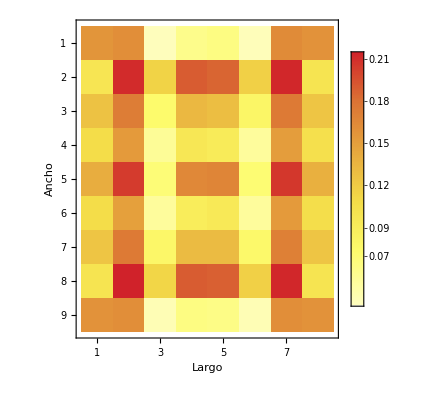

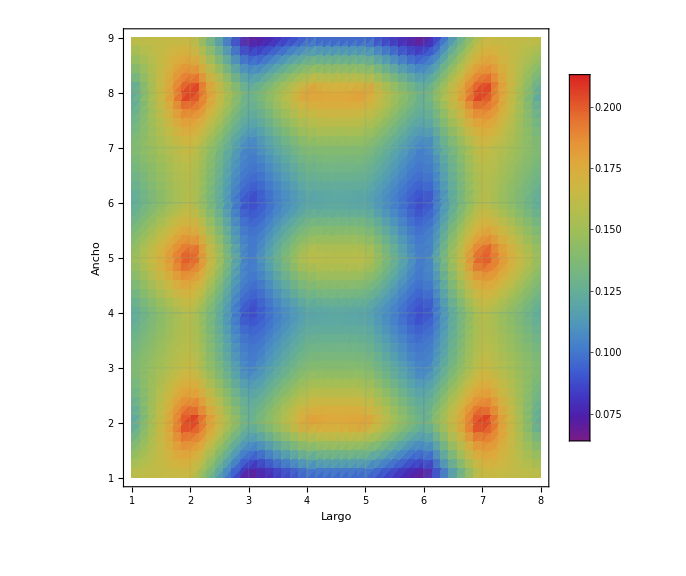

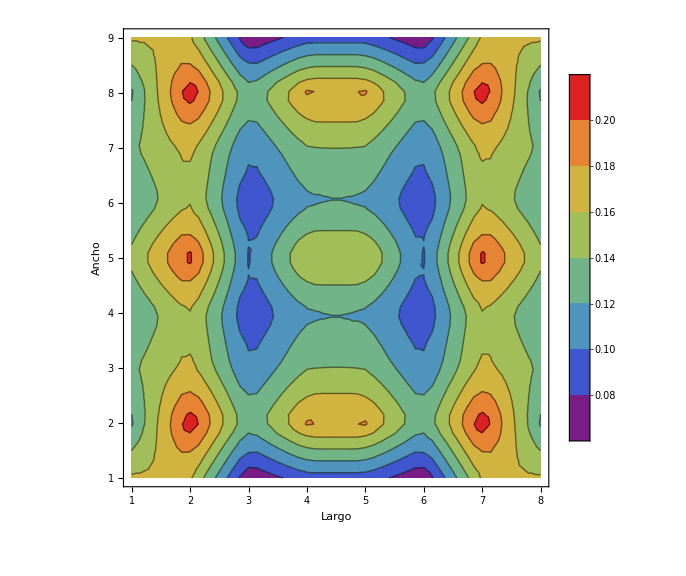

```mathematica
(*LDOS en Espacio REAL*)
Print[     Style["LDOS",18,Bold,Purple]      ]
EnVal=-1.76;
NEn=1.+ ( EnVal-EnMin ) /DEn; 


LDOSRealMatrix=     Table[              SparseArray[  {{i_,i_}->0.},{NZigzag,NArmchair}  ]            , {j,1,NEnPuntos,1}];
Do[         Do[       LDOSRealMatrix [[j,       Mod[ i,NZigzag,1.]  ,   1.+IntegerPart[   (i-1)/NZigzag  ]   ]]=Re[  LDOS [[j,i]]  ]      ,   {i,1,NEdos,1.}]            , {j,1,NEnPuntos,1}];

MatrixPlot[     LDOSRealMatrix [[NEn]]   ,PlotTheme->"Detailed",ColorFunction->"TemperatureMap",FrameLabel->{{"Largo",HoldForm["=E  "]En},{"Ancho",None}}]


LDOSRealDensity=     Table[              Table[  {  1.+IntegerPart[   (i-1)/NZigzag  ],  Mod[ i,NZigzag,1.],    Re[  LDOS [[j,i]]  ]} ,   {i,1,NEdos,1.}]           , {j,1,NEnPuntos,1}];

ListDensityPlot[     LDOSRealDensity [[NEn]]      ,FrameLabel->{{"Ancho",StringTemplate["E = `1` t"][En]},{"Largo",None}}, ImageSize->Large,ColorFunction->"Rainbow",InterpolationOrder->1, MaxPlotPoints->50, Mesh->{6,7},PlotLegends->Automatic]
ListContourPlot[     LDOSRealDensity [[NEn]]      ,FrameLabel->{{"Ancho",StringTemplate["E = `1` t"][En]},{"Largo",None}}, ImageSize->Large,ColorFunction->"Rainbow",InterpolationOrder->1, MaxPlotPoints->50, Mesh->{6,7},PlotLegends->Automatic]
```

Corriente Total

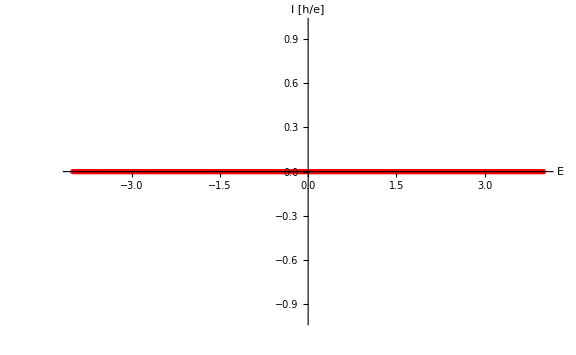

```mathematica
(********** -------- Corriente -------- **********)
Print[     Style["Corriente Total",18,Bold,Purple]      ]
fFermi2=1;           (*Suponiendo Funciones de Fermi iguales a 1*)
SigmaDispersiva=GammaDrenante;         (*Energías de Dispersión, In-Scattering*)
FGreenIn=     Table[               FGreen[[i]] .  SigmaDispersiva.  ConjugateTranspose[   FGreen[[i]]  ]            , {i,1,NEnPuntos,1}];         (*Funcion de Green de Dispersión*)
IVal=    Table[              Im[  2*FGreenIn[[i]]*fFermi2  ]            , {i,1,NEnPuntos,1}];          (*Matrices con los valores de las corrientes*)
ITotal=    Table[           { EnMin  +  DEn*(i-1)   ,         Tr[  IVal[[i]]  ]      }          , {i,1,NEnPuntos,1}];      (*Corriente Total en Función de la Energía: Unidades (h/e)*)


ListPlot[       ITotal     ,PlotStyle->{{PointSize[0.0065],Red}},LabelStyle->{14,Black},AxesLabel->{"E" ,"I [h/e]"}, ImageSize->Large]
```

```mathematica
EnergiasValores
```

{-4.,-3.984,-3.968,-3.952,-3.936,-3.92,-3.904,-3.888,-3.872,-3.856,-3.84,-3.824,-3.808,-3.792,-3.776,-3.76,-3.744,-3.728,-3.712,-3.696,-3.68,-3.664,-3.648,-3.632,-3.616,-3.6,-3.584,-3.568,-3.552,-3.536,-3.52,-3.504,-3.488,-3.472,-3.456,-3.44,-3.424,-3.408,-3.392,-3.376,-3.36,-3.344,-3.328,-3.312,-3.296,-3.28,-3.264,-3.248,-3.232,-3.216,-3.2,-3.184,-3.168,-3.152,-3.136,-3.12,-3.104,-3.088,-3.072,-3.056,-3.04,-3.024,-3.008,-2.992,-2.976,-2.96,-2.944,-2.928,-2.912,-2.896,-2.88,-2.864,-2.848,-2.832,-2.816,-2.8,-2.784,-2.768,-2.752,-2.736,-2.72,-2.704,-2.688,-2.672,-2.656,-2.64,-2.624,-2.608,-2.592,-2.576,-2.56,-2.544,-2.528,-2.512,-2.496,-2.48,-2.464,-2.448,-2.432,-2.416,-2.4,-2.384,-2.368,-2.352,-2.336,-2.32,-2.304,-2.288,-2.272,-2.256,-2.24,-2.224,-2.208,-2.192,-2.176,-2.16,-2.144,-2.128,-2.112,-2.096,-2.08,-2.064,-2.048,-2.032,-2.016,-2.,-1.984,-1.968,-1.952,-1.936,-1.92,-1.904,-1.888,-1.872,-1.856,-1.84,-1.824,-1.808,-1.792,-1.776,-1.76,-1.744,-1.728,-1.712,-1.696,-1.68,-1.664,-1.648,-1.632,-1.616,-1.6,-1.584,-1.568,-1.552,-1.536,-1.52,-1.504,-1.488,-1.472,-1.456,-1.44,-1.424,-1.408,-1.392,-1.376,-1.36,-1.344,-1.328,-1.312,-1.296,-1.28,-1.264,-1.248,-1.232,-1.216,-1.2,-1.184,-1.168,-1.152,-1.136,-1.12,-1.104,-1.088,-1.072,-1.056,-1.04,-1.024,-1.008,-0.992,-0.976,-0.96,-0.944,-0.928,-0.912,-0.896,-0.88,-0.864,-0.848,-0.832,-0.816,-0.8,-0.784,-0.768,-0.752,-0.736,-0.72,-0.704,-0.688,-0.672,-0.656,-0.64,-0.624,-0.608,-0.592,-0.576,-0.56,-0.544,-0.528,-0.512,-0.496,-0.48,-0.464,-0.448,-0.432,-0.416,-0.4,-0.384,-0.368,-0.352,-0.336,-0.32,-0.304,-0.288,-0.272,-0.256,-0.24,-0.224,-0.208,-0.192,-0.176,-0.16,-0.144,-0.128,-0.112,-0.096,-0.08,-0.064,-0.048,-0.032,-0.016,0.,0.016,0.032,0.048,0.064,0.08,0.096,0.112,0.128,0.144,0.16,0.176,0.192,0.208,0.224,0.24,0.256,0.272,0.288,0.304,0.32,0.336,0.352,0.368,0.384,0.4,0.416,0.432,0.448,0.464,0.48,0.496,0.512,0.528,0.544,0.56,0.576,0.592,0.608,0.624,0.64,0.656,0.672,0.688,0.704,0.72,0.736,0.752,0.768,0.784,0.8,0.816,0.832,0.848,0.864,0.88,0.896,0.912,0.928,0.944,0.96,0.976,0.992,1.008,1.024,1.04,1.056,1.072,1.088,1.104,1.12,1.136,1.152,1.168,1.184,1.2,1.216,1.232,1.248,1.264,1.28,1.296,1.312,1.328,1.344,1.36,1.376,1.392,1.408,1.424,1.44,1.456,1.472,1.488,1.504,1.52,1.536,1.552,1.568,1.584,1.6,1.616,1.632,1.648,1.664,1.68,1.696,1.712,1.728,1.744,1.76,1.776,1.792,1.808,1.824,1.84,1.856,1.872,1.888,1.904,1.92,1.936,1.952,1.968,1.984,2.,2.016,2.032,2.048,2.064,2.08,2.096,2.112,2.128,2.144,2.16,2.176,2.192,2.208,2.224,2.24,2.256,2.272,2.288,2.304,2.32,2.336,2.352,2.368,2.384,2.4,2.416,2.432,2.448,2.464,2.48,2.496,2.512,2.528,2.544,2.56,2.576,2.592,2.608,2.624,2.64,2.656,2.672,2.688,2.704,2.72,2.736,2.752,2.768,2.784,2.8,2.816,2.832,2.848,2.864,2.88,2.896,2.912,2.928,2.944,2.96,2.976,2.992,3.008,3.024,3.04,3.056,3.072,3.088,3.104,3.12,3.136,3.152,3.168,3.184,3.2,3.216,3.232,3.248,3.264,3.28,3.296,3.312,3.328,3.344,3.36,3.376,3.392,3.408,3.424,3.44,3.456,3.472,3.488,3.504,3.52,3.536,3.552,3.568,3.584,3.6,3.616,3.632,3.648,3.664,3.68,3.696,3.712,3.728,3.744,3.76,3.776,3.792,3.808,3.824,3.84,3.856,3.872,3.888,3.904,3.92,3.936,3.952,3.968,3.984,4.}

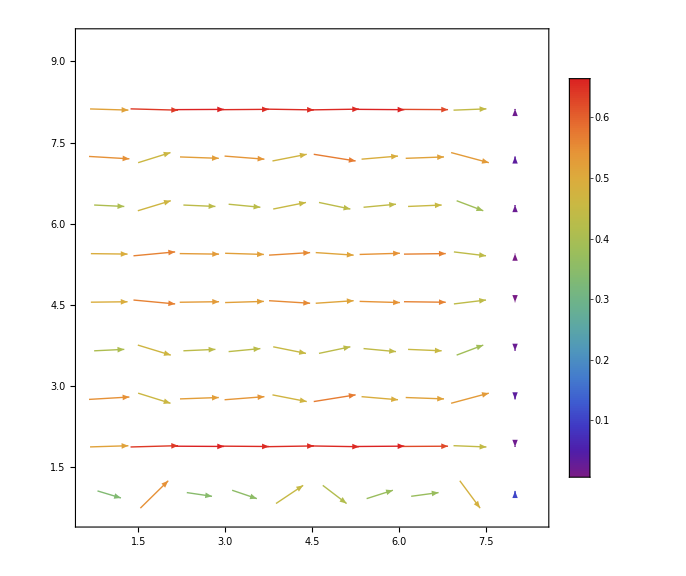

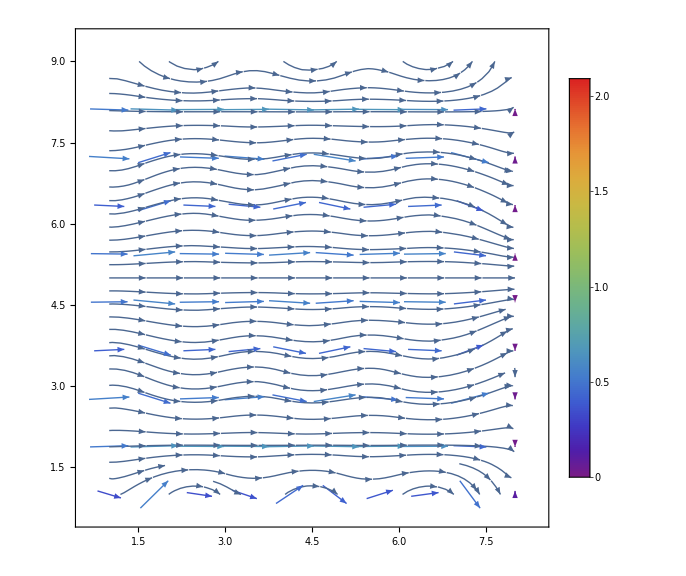

```mathematica
(*Corriente LOCAL*)
EnVal=-1.76;
NEn=1.+ ( EnVal-EnMin ) /DEn; 

IVal[[  NEn  ]] // MatrixForm;


ILocalY=Table[         Table[     -IVal[[NEn,il,  (jl-1)*NZigzag+Mod[il-1,NZigzag,1]  ]]+ IVal[[NEn,il, (jl-1)*NZigzag+Mod[il+1,NZigzag,1]   ]]     , {il, 1+(jl-1)*NZigzag,jl*NZigzag,1}]    , {jl,1,NArmchair,1}];
ILocalY=Flatten[ ILocalY];

ILocalX=   Join[     Table[    IVal[[NEn,il,il+NZigzag ]]     ,{il,1,NZigzag*(NArmchair-1),1}  ] , Table[ 0., {jl,1,NZigzag,1}]      ];



ILocal=              Table[  {       {  1.+IntegerPart[   (i-1)/(NZigzag ) ],  Mod[ i,NZigzag,1.]     }   ,       {ILocalX[[i]],  ILocalY[[i]] }    } ,   {i,1, NEdos,1.}];     


ListVectorPlot[      ILocal     ,ImageSize->Large, VectorColorFunction->"Rainbow",VectorPoints->10, VectorScale->0.08, PlotLegends->Automatic]
ListStreamPlot[      ILocal     ,ImageSize->Large, VectorColorFunction->"Rainbow", VectorPoints->10, VectorScale->0.08, PlotLegends->Automatic]
```